```mathematica
Needs["Constants`"]
Needs["Capture`"]
Needs["Utilities`"]
Needs["EnergyLoss`"]
Needs["Dielectrics`"]
```

## Δr

#### Read EL dicts

Nuclear

```mathematica
FeNuc0ELDict=ReadIt[NotebookDirectory[]<>"../nuclear/FeNuc0ELOutputDict"];
MgNuc0ELDict=ReadIt[NotebookDirectory[]<>"../nuclear/MgNuc0ELOutputDict"];
SiNuc0ELDict=ReadIt[NotebookDirectory[]<>"../nuclear/SiNuc0ELOutputDict"];
ONuc0ELDict=ReadIt[NotebookDirectory[]<>"../nuclear/ONuc0ELOutputDict"];
```

Electronic

```mathematica
(*FeeELDict=ReadIt[NotebookDirectory[]<>"../ELandKappamin/compute energy loss/FeELOutputDictSIwiderm"];
SiO2eELDict=ReadIt[NotebookDirectory[]<>"../ELandKappamin/compute energy loss/SiO2ELOutputDictSIwiderm"];
MgOeELDict=ReadIt[NotebookDirectory[]<>"../ELandKappamin/compute energy loss/MgOELOutputDictSIwiderm"];*)
FeeELDict=ReadIt[NotebookDirectory[]<>"../ELandKappamin/compute energy loss/FeELOutputDictSIEnhanced"];
SiO2eELDict=ReadIt[NotebookDirectory[]<>"../ELandKappamin/compute energy loss/SiO2ELOutputDictSIEnhanced"];
MgOeELDict=ReadIt[NotebookDirectory[]<>"../ELandKappamin/compute energy loss/MgOELOutputDictSIEnhanced"];
```

#### Interpolation test

```mathematica
SiO2eELDict[["f"]]=TestInterpolation[SiO2eELDict]
MgOeELDict[["f"]]=TestInterpolation[MgOeELDict]
```

Set::noval: Symbol SiO2eELDict in part assignment does not have an immediate value.

TestInterpolation[SiO2eELDict]

Set::noval: Symbol MgOeELDict in part assignment does not have an immediate value.

TestInterpolation[MgOeELDict]

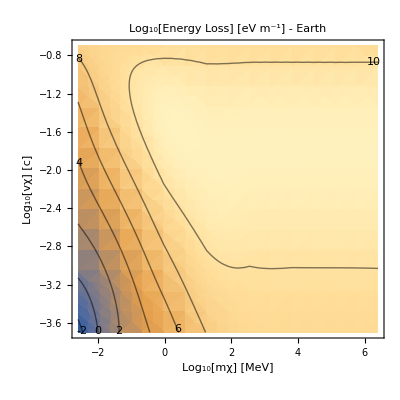

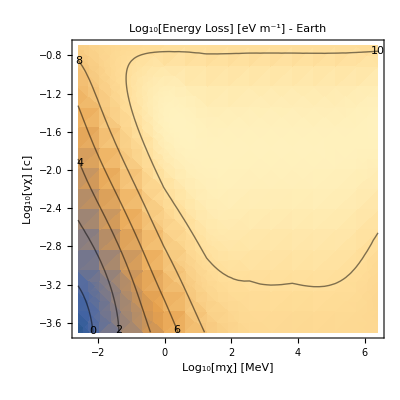

```mathematica
PlotEL[SiO2eELDict]
PlotEL[MgOeELDict]
```

#### EL functions

Organize into an EL function

Mantle

```mathematica
fTot0ELMantle[mχ_,vχ_]:= Log10["SiO2Frac"(10^SiO2eELDict[["f"]][mχ,vχ]+10^SiNuc0ELDict[["f"]][mχ,vχ]+2 10^ONuc0ELDict[["f"]][mχ,vχ])+"MgOFrac"(10^MgOeELDict[["f"]] [mχ,vχ]+10^MgNuc0ELDict[["f"]][mχ,vχ]+ 10^ONuc0ELDict[["f"]][mχ,vχ])]/.EarthRepl
feELMantle[mχ_,vχ_]:= Log10["SiO2Frac"(("ρM")/("ρSiO2")/.MassDensities)(10^SiO2eELDict[["f"]][mχ,vχ])+"MgOFrac"(("ρM")/("ρMgO")/.MassDensities)(10^MgOeELDict[["f"]] [mχ,vχ])]/.EarthRepl (*ignores slight change in densities from surface to mantle in densities (we showed it's irrelevant for iron in the core, so it will be even less significant here)*)
```

Core

```mathematica
fTot0ELCore[mχ_,vχ_]:=Log10[10^FeeELDict[["f"]][mχ,vχ] + 10^FeNuc0ELDict[["f"]][mχ,vχ]]
feELCore[mχ_,vχ_]:=FeeELDict[["f"]][mχ,vχ]
```

```mathematica
FeeELDict[["f"]]
```

InterpolatingFunction[…]

```mathematica
FeNuc0ELDict[["f"]][-32.3,4.8]
FeNuc0ELDict[["f"]][-32.3,4.8]
```

-3.42349

```mathematica
10^-32("c")^2/("JpereV")/.SIConstRepl
10^-23("c")^2/("JpereV")/.SIConstRepl
```

5617.98

5.61798×10^12

### Test initialization functions

#### Propagating to the Earth

```mathematica
EK∞[mχ_,v∞_]:= 1/2 mχ (v∞)^2
```

```mathematica
E∞[mχ_,v∞_,r∞_,V_]:=EK∞[mχ,v∞]+V[r∞]
```

```mathematica
E∞[mχ,v∞,r∞,V[x,y,#]&]
```

EK∞[mχ,v∞]+V[x,y,r∞]

```mathematica
Vtest[r_]:=Gα/r
E∞[mχ,v∞,r∞,Vtest]
```

Gα/(r∞)+(mχ (v∞)^2)/2

```mathematica
vperp[v∞_,b∞_,r_]:=(b∞ v∞)/r
```

```mathematica
vr[mχ_,v∞_,b∞_,r∞_,V_,r_]:=√(2/mχ(E∞[mχ,v∞,r∞,V]-V[r])-vperp[v∞,b∞,r]^2)
```

```mathematica
vr[mχ,v∞,b∞,r∞,V,r]
```

√(-((b∞)^2 (v∞)^2)/r^2+(2 ((mχ (v∞)^2)/2-V[r]+V[r∞]))/mχ)

```mathematica
br[mχ_,v∞_,b∞_,r∞_,V_,r_]:=(b∞)/(√(1+(V[r∞]-V[r])/(EK∞[mχ,v∞])))
```

```mathematica
br[mχ,v∞,b∞,r∞,V,r]
```

(b∞)/(√(1+(2 (-V[r]+V[r∞]))/(mχ (v∞)^2)))

```mathematica
"G"/.SIConstRepl
```

6.67×10^-11

```mathematica
Vgrav[r_,mχ_] :=- (mχ("G"/.SIConstRepl)("ME"/.EarthRepl))/r
```

```mathematica
Vgrav[#,mχ]&
%[r]
```

Vgrav[#1,mχ]&

-(3.98199×10^14 mχ)/r

#### Example of Initial conditions

```mathematica
1/("rE"/.EarthRepl)br["m"/.SIConstRepl,"c"10^-3/.SIConstRepl,0.5 "rE"/.EarthRepl,10^4 "rE"/.EarthRepl,Vgrav[#,"m"/.SIConstRepl]&,"rE"/.EarthRepl]
```

0.499653

so barely changed, electrons are fast, but did decrease (which is the right direction)

```mathematica
vr["m"/.SIConstRepl,"c"10^-3/.SIConstRepl,0.5 "rE"/.EarthRepl,10^4 "rE"/.EarthRepl,Vgrav[#,"m"/.SIConstRepl]&,"rE"/.EarthRepl]
```

260048.

```mathematica
vperp["c"10^-3/.SIConstRepl,0.5 "rE"/.EarthRepl,"rE"/.EarthRepl]
```

150000.

#### Δr

```mathematica
Clear[Δrtest]
Δrtest[mχ_,vχ_,κ_,y_,consts_] :=(y 1/2 mχ vχ^2)/(κ^2 "JpereV"10^fELMantle[Log10[mχ], Log10[vχ]]) /.consts
```

```mathematica
Δrtest["m"/.SIConstRepl,"c"10^-3/.SIConstRepl,10^-9,10^-2,SIConstRepl]
%/("rE"/.EarthRepl)
```

1734.54

0.000272255

```mathematica
dE[rE_,bE_]:=2 √(rE^2-bE^2)
```

```mathematica
dE["rE"/.EarthRepl,0.5"rE"/.EarthRepl]
```

1.10349×10^7

```mathematica
N[1/500]
```

0.002

```mathematica
Δrtest["m"/.SIConstRepl,"c"10^-3/.SIConstRepl,10^-10,10^-2,SIConstRepl]/dE["rE"/.EarthRepl,0.5"rE"/.EarthRepl]
```

0.0157187

So at 10^-10mixing at electron mass and halo speeds, with b∞ = 1/2 rE, we are in intermediate scattering regime

#### Δr generalised (e only)

```mathematica
dc[bE_] := 2 √(rcore^2-bE^2)
dE[bE_] := 2 √(REarth^2-bE^2)
dM[bE_]:= If[rcore^2>bE^2,dE[bE] - dc[bE],Re[dE[bE]]]
```

```mathematica
dM[0]+dc[0]
REarth 2
```

1.2742×10^7

1.2742×10^7

```mathematica
EK[mχ_,vχ_] :=1/2 mχ vχ^2
ΔEe[mχ_,vχ_,κ_,bE_,consts_] :=(κ^2 "JpereV"(dM[bE] 10^feELMantle[Log10[mχ], Log10[vχ]]+dc[bE] 10^feELCore[Log10[mχ], Log10[vχ]])) /.consts
(*EKbyΔEe[mχ_,vχ_,κ_,bE_,consts_] :=(  1/2 mχ vχ^2)/(κ^2 "JpereV"(dM[bE] 10^feELMantle[Log10[mχ], Log10[vχ]]+dc[bE] 10^feELCore[Log10[mχ], Log10[vχ]])) /.consts (* energy lost after travelling through the Earth over kinetic enrgy *)*)
EKbyΔEe[mχ_,vχ_,κ_,bE_,consts_] := EK[mχ,vχ]/ΔEe[mχ,vχ,κ,bE,consts]
ΔrAveraged[mχ_,vχ_,κ_,y_,bE_,consts_]:= dE[bE] y EK[mχ,vχ]/ΔEe[mχ,vχ,κ,bE,consts]
fΔrAveraged[mχ_,vχ_]:=Log10[ΔrAveraged[10^mχ,10^vχ,1,10^-2,0,SIConstRepl]^-1]
```

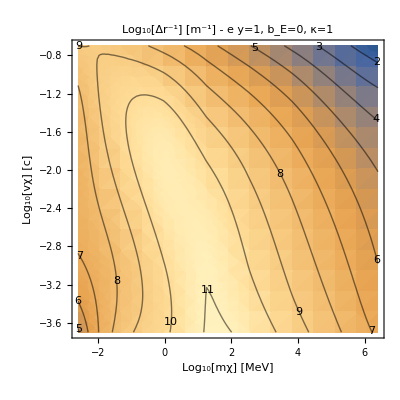

```mathematica
Block[{tempDict},
tempDict=FeeELDict;
tempDict[["f"]]=fΔrAveraged;
PlotEL[tempDict,"",True,"Log_10[Δr^-1] [m^-1] - e y=1, b_E=0, κ=1"]
]
```

#### Δr total

```mathematica
ΔETot0[mχ_,vχ_,κ_,bE_,consts_] :=(κ^2 "JpereV"(dM[bE] 10^fTot0ELMantle[Log10[mχ], Log10[vχ]]+dc[bE] 10^fTot0ELCore[Log10[mχ], Log10[vχ]])) /.consts
(*EKbyΔEe[mχ_,vχ_,κ_,bE_,consts_] :=(  1/2 mχ vχ^2)/(κ^2 "JpereV"(dM[bE] 10^feELMantle[Log10[mχ], Log10[vχ]]+dc[bE] 10^feELCore[Log10[mχ], Log10[vχ]])) /.consts (* energy lost after travelling through the Earth over kinetic enrgy *)*)
EKbyΔETot0[mχ_,vχ_,κ_,bE_,consts_] := EK[mχ,vχ]/ΔETot0[mχ,vχ,κ,bE,consts]
ΔrAveragedTot0[mχ_,vχ_,κ_,y_,bE_,consts_]:= dE[bE] y EK[mχ,vχ]/ΔETot0[mχ,vχ,κ,bE,consts]
(*fΔrAveragedTot0[mχ_,vχ_]:=Log10[ΔrAveragedTot0[10^mχ,10^vχ,1,10^-2,0,SIConstRepl]^-1]*)
fΔrAveragedTot0[mχ_,vχ_]:=Log10[ΔrAveragedTot0[10^mχ,10^vχ,1,10^-2,0,SIConstRepl]^-1]
```

```mathematica
FeeELDict[["kinlist"]][["mχ"]]("c")^2/("JpereV")/.SIConstRepl
```

{2500.,48267.4,931898.,1.79921×10^7,3.47374×10^8,6.70674×10^9,1.29487×10^11,2.5×10^12}

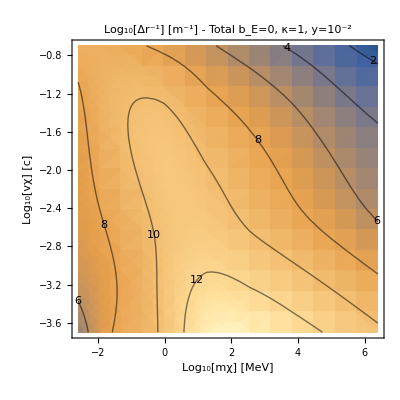

```mathematica
Block[{tempDict},
tempDict=FeeELDict;
tempDict[["f"]]=fΔrAveragedTot0;
PlotEL[tempDict,"",True,"Log_10[Δr^-1] [m^-1] - Total b_E=0, κ=1, y=10^-2"]
]
```

4.81365+6.04929×10^-19 ⅈ

-3.69897

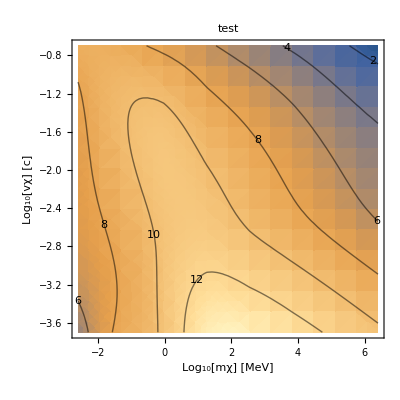

```mathematica
Block[{ELdict},
ELdict=FeeELDict;
ELdict[["f"]]=fΔrAveragedTot0;
(*PlotEL[tempDict,"",True,"Log_10[Δr^-1] [m^-1] - Total b_E=0, κ=1, y=10^-2"]*)
Print[ELdict[["f"]][Log[10,First[ELdict[["kinlist"]][["mχ"]]]],Log[10,First[ELdict[["kinlist"]][["vχ"]]]]]];
Print[N[Log[10,First[ELdict[["kinlist"]][["vχ"]]]]-Log10["c"/.Constants`SIConstRepl]]];
Print[Show[{DensityPlot[Re[ELdict[["f"]][m+6 - Log10[("c"^2)/("JpereV")/.Constants`SIConstRepl],v +Log10["c"/.Constants`SIConstRepl]]],
  		{m,Log[10,First[ELdict[["kinlist"]][["mχ"]]]]-6 + Log10[("c")^2/("JpereV")/.Constants`SIConstRepl],Log[10,Last[ELdict[["kinlist"]][["mχ"]]]]-6 + Log10[("c")^2/("JpereV")/.Constants`SIConstRepl]},
  		{v,Log[10,First[ELdict[["kinlist"]][["vχ"]]]]-Log10["c"/.Constants`SIConstRepl],Log[10,Last[ELdict[["kinlist"]][["vχ"]]]]-Log10["c"/.Constants`SIConstRepl]},
  		FrameLabel->{"\!\(\*SubscriptBox[\(Log\), \(10\)]\)[mχ] [MeV]","\!\(\*SubscriptBox[\(Log\), \(10\)]\)[vχ] [c]"},PlotLabel->"test"],
  ContourPlot[Re[ELdict[["f"]][m+6- Log10[("c")^2/("JpereV")/.Constants`SIConstRepl],v+Log10["c"/.Constants`SIConstRepl]]],
  		{m,Log[10,First[ELdict[["kinlist"]][["mχ"]]]]-6 + Log10[("c")^2/("JpereV")/.Constants`SIConstRepl],Log[10,Last[ELdict[["kinlist"]][["mχ"]]]]-6 + Log10[("c")^2/("JpereV")/.Constants`SIConstRepl]},
  		{v,Log[10,First[ELdict[["kinlist"]][["vχ"]]]]-Log10["c"/.Constants`SIConstRepl],Log[10,Last[ELdict[["kinlist"]][["vχ"]]]]-Log10["c"/.Constants`SIConstRepl]},
  		ContourLabels->True,ContourShading->False]}]]
]
```

#### Explain boundary and peak (lowest kinetic energy above the fermi energy)

```mathematica
("EF")/("JpereV") /.FeeELDict[["fitparams"]]
("EF")/("JpereV") /.SiO2eELDict[["fitparams"]]
("EF")/("JpereV") /.MgOeELDict[["fitparams"]]
```

{8.0607,12.1265,20.9318,78.9,2030.5,42688.4}

{20.0443,58.1666}

{10.3207,18.4045,21.0279,50.3071}

```mathematica
((10^-2.5 "c")^2"m")/("JpereV") /.FeeELDict[["fitparams"]]
((10^-1.5 "c")^2 10^-2"m")/("JpereV") /.FeeELDict[["fitparams"]]
```

{5.11798,5.11798,5.11798,5.11798,5.11798,5.11798}

{5.11798,5.11798,5.11798,5.11798,5.11798,5.11798}

#### Interaction Length

```mathematica
Block[{mχtemp,vχtemp,ωmaxtemp},
mχtemp = 5 10^5 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 10^-3 "c"/.SIConstRepl;
ωmaxtemp = 1/(2"ℏ")mχtemp vχtemp^2/.SIConstRepl;
Print[dσdERe[# ωmaxtemp,mχtemp,
vχtemp,FeeELDict[["fitparams"]],βcore]& [1/2]];
(*NIntegrate[dσdEReNum[ω,mχtemp,vχtemp,FeTotalparams,βcore],{ω,0,ωmaxtemp}]*)
]
```

0.0262616

tesing cell input

```mathematica
σFe = 1.085089955014962*^13
```

1.08509×10^13

```mathematica
σtemp = 0;
Block[{mχtemp,vχtemp,ωmaxtemp},
mχtemp = 5 10^5 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 10^-3 "c"/.SIConstRepl;
ωmaxtemp = 1/(2"ℏ")mχtemp vχtemp^2/.SIConstRepl;
Print[dσdERe[# ωmaxtemp,mχtemp,vχtemp,FeTotalparams,βcore]& []];
(*σtemp = NIntegrate[dPdωeNum[ω,mχtemp,vχtemp,SiO2Totalparams],{ω,0,ωmaxtemp}]*)
]
```

0

```mathematica
lFe = κ^2("nI"/.SIcoreparams)σFe /.κ->10^-10(*approx, should really do density of each shell*)
```

1.52116×10^22

1.51848×10^15

0.

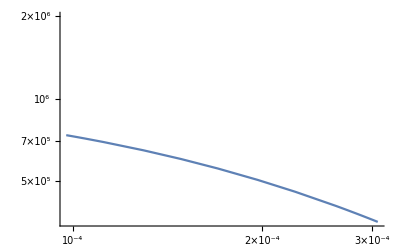

```mathematica
σtemp=0;
Block[{mχtemp,vχtemp,ωmaxtemp},
mχtemp = 2 10^6 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 10^-3 "c"/.SIConstRepl;
ωmaxtemp = 1/(2"ℏ")mχtemp vχtemp^2/.SIConstRepl;
Print[ωmaxtemp];
Print[dPdωNuc0Num[1/10 ωmaxtemp,mχtemp,vχtemp,SiNucCoeffs,SIConstRepl,<|"nI"->nIFromDensity[3580,"mN"/.SiNucCoeffs]|>]];
Print[LogLogPlot[dPdωNuc0Num[ω ωmaxtemp,mχtemp,vχtemp,SiNucCoeffs,SIConstRepl,<|"nI"->nIFromDensity[3580,"mN"/.SiNucCoeffs]|>],{ω,0,10^-1},PlotRange->{0,2 10^6}]];
(*σtemp = NIntegrate[dPdωNuc0Num[ω,mχtemp,vχtemp,SiNucCoeffs,SIConstRepl,<|"nI"->nIFromDensity[3580,"mN"/.SiNucCoeffs]|>],{ω,0,ωmaxtemp}]*)
]
```

```mathematica
nIFromDensity[3580, "mN" /. SiNucCoeffs]
```

7.70224×10^28

```mathematica
1/(2 "ℏ")(2.5 10^7 ("JpereV")/("c")^2) (2.5 10^-5 "c")^2/.SIConstRepl
```

1.18632×10^13

```mathematica
SIcoreparams
```

{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→1.1215×10^30,qF→3.2142×10^10,vF→3.72227×10^6,μ→6.31108×10^-18,ωp→5.97822×10^16,α→1/137,χ→0.432735,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→83.5454,nI→1.40188×10^29,Z→8,M→9.27329×10^-26,EF→6.31108×10^-18}

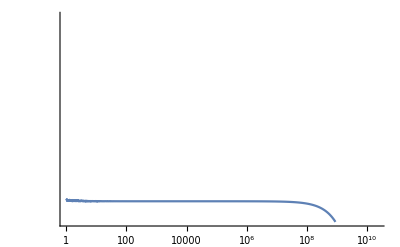

```mathematica
LogLogPlot[dPdωNuc0[ω,2.5 10^7 ("JpereV")/("c")^2/.SIConstRepl,2.5 10^-5 "c"/.SIConstRepl,FeNucCoeffs,SIConstRepl,<|"nI"->("nI"/.SIcoreparams)|>],{ω,10^0,10^15},PlotRange->{0,2.5 10^8}]
```

```mathematica
σtemp=0;
Block[{mχtemp,vχtemp,ωmaxtemp},
mχtemp = 2 10^6 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 10^-3 "c"/.SIConstRepl;
ωmaxtemp = 1/(2"ℏ")mχtemp vχtemp^2/.SIConstRepl;
Print[ωmaxtemp];
Print[dPdωNuc0Num[1/10 ωmaxtemp,mχtemp,vχtemp,SiNucCoeffs,SIConstRepl,<|"nI"->nIFromDensity[3580,"mN"/.SiNucCoeffs]|>]];
(*Print[LogLogPlot[dPdωNuc0Num[ω ωmaxtemp,mχtemp,vχtemp,SiNucCoeffs,SIConstRepl,<|"nI"->nIFromDensity[3580,"mN"/.SiNucCoeffs]|>],{ω,0,10^-1},PlotRange->{0,2 10^6}]];*)
(*σtemp = NIntegrate[dPdωNuc0Num[ω,mχtemp,vχtemp,SiNucCoeffs,SIConstRepl,<|"nI"->nIFromDensity[3580,"mN"/.SiNucCoeffs]|>],{ω,0,ωmaxtemp}]*)
]
σtemp = 0;
Clear[SiNuc0σ]
SiNuc0P[mχtemp_,vχtemp_]:=Module[{ωRmaxtemp,EKtemp,mNtemp},
(*{mχtemp,vχtemp,ωRmaxtemp,EKtemp,mNtemp},*)
(*mχtemp = 5 10^5 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 10^-3 "c"/.SIConstRepl;*)
EKtemp = 1/2 mχtemp vχtemp^2;
mNtemp = "mN"/.SiNucCoeffs;
ωRmaxtemp=EKtemp/("ℏ") (4 mNtemp mχtemp)/(mNtemp + mχtemp)^2/.SIConstRepl;
Print[ωRmaxtemp];
NIntegrate[dPdωNuc0Num[ω,mχtemp,vχtemp,SiNucCoeffs,SIConstRepl,<|"nI"->nIFromDensity[3580,mNtemp]|>],{ω,0,ωRmaxtemp}]
]
SiNuc0PTot=SiNuc0P[5 10^5 ("JpereV")/("c")^2/.SIConstRepl,10^-3 "c"/.SIConstRepl]
```

1.51848×10^15

0.

2.90748×10^10

3.15401×10^16

```mathematica
((κ^2/.κ->10^-10)SiNuc0PTot)/((nIFromDensity[3580,"mN"/.SiNucCoeffs])("ℏ"/.SIConstRepl)(10^-3 "c"/.SIConstRepl))
```

0.000129382

9.5117×10^8

```mathematica
SiNuc0P[mχtemp_,vχtemp_]:=Module[{ωRmaxtemp,EKtemp,mNtemp},
(*{mχtemp,vχtemp,ωRmaxtemp,EKtemp,mNtemp},*)
(*mχtemp = 5 10^5 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 10^-3 "c"/.SIConstRepl;*)
EKtemp = 1/2 mχtemp vχtemp^2;
mNtemp = "mN"/.SiNucCoeffs;
ωRmaxtemp=EKtemp/("ℏ") (4 mNtemp mχtemp)/(mNtemp + mχtemp)^2/.SIConstRepl;
Print[ωRmaxtemp];
NIntegrate[dPdωNuc0Num[ω,mχtemp,vχtemp,SiNucCoeffs,SIConstRepl,<|"nI"->nIFromDensity[3580,mNtemp]|>],{ω,0,ωRmaxtemp}]
]
SiNuc0PTot=SiNuc0P[5 10^5 ("JpereV")/("c")^2/.SIConstRepl,10^-3 "c"/.SIConstRepl]
SiNuc0Pλ=(((κ^2/.κ->10^-10)SiNuc0PTot)/(10^-3 "c"/.SIConstRepl))^-1
```

2.90748×10^10

3.15401×10^16

9.5117×10^8

So from Nuclear Si at 0 temperature, the scattering length is large compared to the Earth

```mathematica
dPdωNuc0Num[# ωmaxtemp,mχtemp,vχtemp,SiNucCoeffs,SIConstRepl,<|"nI"->nIFromDensity[3580,"mN"/.SiNucCoeffs]|>]& [1/2]
```

```mathematica
SiNucCoeffs
```

<|a→{6.2915,3.0353,1.9891,1.541},b→{2.4386,32.3337,0.6785,81.6937},c→1.1407,Z→13.9976,A→28,rn→3.46171×10^-15,mN→4.648×10^-26|>

```mathematica
FrontEndTokenExecute@"Save"
```

### Unit testing for MC capture code

Psuedo code

We need to store the following to describe the state of the particle

globally we need 
(r,v_r,v_(⊥1),v_(⊥1)) with b the impact parameter and r the radial position in the earth

at each time step we need
l interaction length
i_int which process to interact with (electrical or nuclear)
velocity of target
	speed of target (sampled from distribution function)
	point on sphere - for velocity of target
E_R recoil energy 
	q momentum transfer
	scattering angle of DM particle
New velocity
	azimuthal angle 
	polar calculated from scattering angle

#### Update v

```mathematica
vr[r_,E_,V_,m_,vp_]:=√(Simplify[2/m E]-2/m V[r]-vp)
V[r_]:=-("α")/r
```

```mathematica
(*Clear[modv,Δt,vr]*)
Block[{m,r,v={vr,vp1,vp2},l,speed,Δt,Δr,L,vp,E},
speed = √(v.v);
Δt = l/speed;
Δr = Δt v[[1]];

E=m/2 speed^2;
vp = v.DiagonalMatrix[{0,1,1}].v;
(*L = m r vp;*)
v[[1]]=vr[r+Δr,E,V,m,vp];
v

]
```

{√(vr^2+(2 α)/(m (r+(l vr)/(√(vp1^2+vp2^2+vr^2))))),vp1,vp2}

```mathematica
√(-vp1^2-vp2^2+(2 (1/2 m (vp1^2+vp2^2+vr^2)-("α")/(r+(l vr)/(√(vp1^2+vp2^2+vr^2)))))/m)
```

#### compute l - interaction length

#### σ

```mathematica
SIConstRepl
```

{e→1.60289×10^-19,m→9.11×10^-31,hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,α→1/137,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,G→6.67×10^-11}

```mathematica
dσdERNuc0[]
```

```mathematica
?dσdERNuc0
```

## new

#### Load parameters

```mathematica
Clear[FeTotalparams,SiO2Totalparams,MgOTotalparams]
```

```mathematica
FeTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/FeTotalparams"];
SiO2Totalparams= ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/SiO2Totalparams"];
MgOTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/MgOTotalparams"];
```

#### Load Interaction Length

```mathematica
Clear[FeλeDictSI,SiO2λeDictSI,MgOλeDictSI]
```

```mathematica
(*FeλeDictSI = ReadIt[NotebookDirectory[]<>"FeλeDictSI"];
SiO2λeDictSI = ReadIt[NotebookDirectory[]<>"SiO2λeDictSI"];
MgOλeDictSI = ReadIt[NotebookDirectory[]<>"MgOλeDictSI"];*)
FeλeDictSI = ReadIt[NotebookDirectory[]<>"FeλeDictSI_total"];
SiO2λeDictSI = ReadIt[NotebookDirectory[]<>"SiO2λeDictSI_total"];
MgOλeDictSI = ReadIt[NotebookDirectory[]<>"MgOλeDictSI_total"];
```

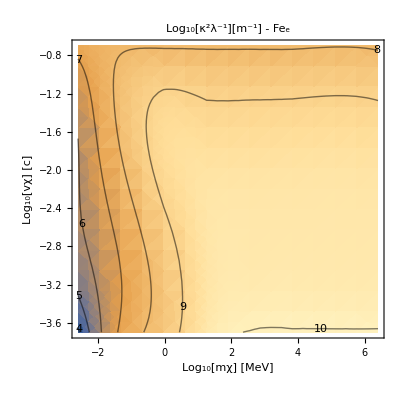

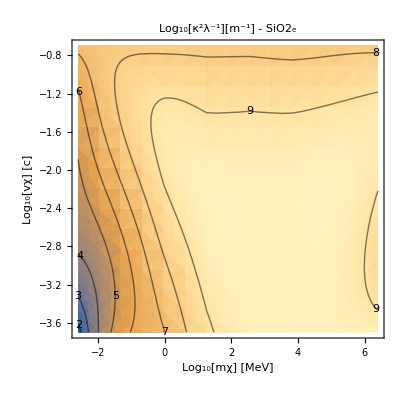

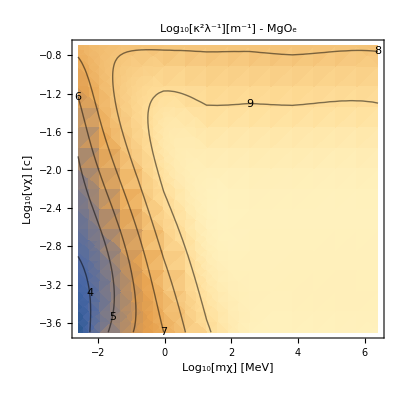

```mathematica
EnergyLoss`PlotEL[FeλeDictSI,"Fe_e",True,"Log_10[κ^2λ^-1][m^-1] - Fe_e"]
EnergyLoss`PlotEL[SiO2λeDictSI,"SiO2_e",True,"Log_10[κ^2λ^-1][m^-1] - SiO2_e"]
EnergyLoss`PlotEL[MgOλeDictSI,"MgO_e",True,"Log_10[κ^2λ^-1][m^-1] - MgO_e"]
```

### Unit Test

#### Interaction length

```mathematica
FeλeDictSI[["f"]]
FeλeDictSI[["f"]][-25,6]
```

InterpolatingFunction[…]

9.69693

```mathematica
(*testl[mχ_,vχ_,κ_,f_,Natural_:False] := Module[{λ,mχnatconv,vχnatconv},
(*f is a log log function from kinematic variables to the inverse interaction length
κ is kinetic mixing
Natural == True is for natural units for kinematic variables ([eV] for mass and [c] for speed])*)
mχnatconv=("JpereV")/("c")^2/.Constants`SIConstRepl;
vχnatconv="c"/.Constants`SIConstRepl;
λ=If[Natural,10^(-f[Log10[mχ mχnatconv],Log10[vχ vχnatconv]]),10^(-f[Log10[mχ],Log10[vχ]])];
-λ/κ^2Log[1-Random[]]
]*)
Clear[testl]
```

```mathematica
Capture`Getl[10^-25,10^5,10^-9,FeλeDictSI[["f"]]]
```

3.10584×10^7

```mathematica
Capture`Getl[10^6,10^-2,10^-9,FeλeDictSI[["f"]],True]
```

9.15873×10^8

```mathematica
SIConstRepl
```

{e→1.60289×10^-19,m→9.11×10^-31,hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,α→1/137,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,G→6.67×10^-11}

5.61798×10^12

```mathematica
("c")^2/("JpereV")10^-23/.SIConstRepl
```

5.61798×10^12

```mathematica
10^5/("c")/.SIConstRepl
```

1/3000

#### Update v

```mathematica
V[r_]:=-(("e")^2/("ϵ0"))/r-("G""ME")/r/.EarthRepl/.SIConstRepl
```

```mathematica
(*Clear[modv,Δt,vr]*)
Block[{m,r,v={vr,vp1,vp2},l,speed,Δt,Δr,L,vp,E},
speed = √(v.v);
Δt = l/speed;
Δr = Δt v[[1]];

E=m/2 speed^2;
vp = v.DiagonalMatrix[{0,1,1}].v;
(*L = m r vp;*)
v[[1]]=vr[r+Δr,E,V,m,vp];
v

]
```

{√(vr^2+(2 α)/(m (r+(l vr)/(√(vp1^2+vp2^2+vr^2))))),vp1,vp2}

```mathematica
√(-vp1^2-vp2^2+(2 (1/2 m (vp1^2+vp2^2+vr^2)-("α")/(r+(l vr)/(√(vp1^2+vp2^2+vr^2)))))/m)
```

```mathematica
(*vr[r_,E_,V_,m_,vp_]:=√(Simplify[(2/m)E]-(2/m)V[r]-vp^2)*)
(*Updatev[vχ_,mχ_,r_,l_,V_]:=Module[{speed,Δt,Δr,vr,L,vp,E,reached},
speed = √(vχ.vχ);
Δt = l/speed;
Δr = Δt vχ[[1]];
E=(mχ/2)speed^2+V[r];
vp = √(vχ.DiagonalMatrix[{0,1,1}].vχ); (*(v_⊥)^2*)
vr=√(Simplify[(2/mχ)E]-(2/mχ)V[r+Δr]-vp^2);(*updated radial velocity*)
(*L = m r vp;*)
(*Print[speed];
Print[Δt];
Print[Δr];
Print[vp];*)
(*vχ[[1]]=vr[Abs[r+Δr],E,V,mχ,vp];*)
(*Print[vr[r+Δr,E,V,mχ,vp]];*)
(*Print[(mχ/2)speed^2+V[r] >V[r+Δr]+(mχ/2)vp^2];*)
reached=(mχ/2)speed^2-(mχ/2)vp^2+V[r] >V[r+Δr];(*check that Energy is high enough to reach r+Δr*)
<|"vχ"->If[reached,{vr[Abs[r+Δr],E,V,mχ,vp],vχ[[2]],vχ[[3]]},{-vχ[[1]],vχ[[2]],vχ[[3]]}],"r"->Abs[r+Δr],"reached?"->reached|>
(*{vr[r+Δr,E,V,mχ,vp],vχ[[2]],vχ[[3]]}*)

]*)
Clear[Updatev,vr]
(*Updatev[vχ_,mχ_,r_,l_,V_]:=Module[{speed,Δt,Δr,vr,L,vp,E,reached},
speed = √(vχ.vχ);
Δt = l/speed;
Δr = Δt vχ[[1]];
E=(mχ/2)speed^2+V[r];
vp = √(vχ.DiagonalMatrix[{0,1,1}].vχ); (*(v_⊥)^2*)
vr=√(Simplify[(2/mχ)E]-(2/mχ)V[Abs[r+Δr]]-vp^2);(*updated radial velocity*)
(*L = m r vp;*)
(*Print[speed];
Print[Δt];
Print[Δr];
Print[vp];*)
(*vχ[[1]]=vr[Abs[r+Δr],E,V,mχ,vp];*)
(*Print[vr[r+Δr,E,V,mχ,vp]];*)
(*Print[(mχ/2)speed^2+V[r] >V[r+Δr]+(mχ/2)vp^2];*)
reached=(mχ/2)speed^2-(mχ/2)vp^2+V[r] >V[Abs[r+Δr]];(*check that Energy is high enough to reach r+Δr*)
<|"vχ"->If[reached,{vr,vχ[[2]],vχ[[3]]},{-vχ[[1]],vχ[[2]],vχ[[3]]}],"r"->Abs[r+Δr],"reached?"->reached,"E"->E,"vp"->vp,"Δr"->Δr,"V[r]"->V[r],"V[|r+Δr|]"->V[Abs[r+Δr]],"l"->l,"vχ"->vχ,"mχ"->N[mχ]|>
(*{vr[r+Δr,E,V,mχ,vp],vχ[[2]],vχ[[3]]}*)

]*)(*******USE THIS VERSION IF THE PACKAGE VERSION STOPS WORKING*)
```

```mathematica
(10^-25 Vgrav[#])&
%[1]
```

Vgrav[#1]/10^25&

-9.37527×10^-18

```mathematica
Capture`Getl[10^-25,10^5,10^-9,FeλeDictSI[["f"]]]
Updatev[{10^3,0,0},10^-25,10^8,%,(10^-25 Vgrav[#])&]
```

3.54856×10^8

<|vχ→{1000,0,0},r→4.54856×10^8,reached?→False,E→-3.48199×10^-19,vp→0,Δr→3.54856×10^8,V[r]→-3.98199×10^-19,V[|r+Δr|]→-8.75439×10^-20,l→3.54856×10^8,mχ→1.×10^-25|>

```mathematica
Capture`Getl[10^-25,10^5,10^-9,FeλeDictSI[["f"]]]
Updatev[{-10^3,0,0},10^-25,10^8,%,(10^-25 Vgrav[#])&]
```

4.3445×10^7

<|vχ→{2667.93,0,0},r→5.6555×10^7,reached?→True,E→-3.48199×10^-19,vp→0,Δr→-4.3445×10^7|>

```mathematica
Capture`Getl[10^-25,10^5,10^-9,FeλeDictSI[["f"]]]
Updatev[{-10^3,0,0},10^-25,10^8,%,(10^-25 Vgrav[#])&]
```

4.23098×10^8

<|vχ→{1000,0,0},r→3.23098×10^8,reached?→False|>

```mathematica
Capture`Getl[10^-25,10^5,10^-9,FeλeDictSI[["f"]]]
Updatev[{-10^3,0,0},10^-25,10^8,%,(10^-25 Vgrav[#])&]
```

1.40354×10^8

<|vχ→{1000,0,0},r→4.03544×10^7,reached?→False|>

```mathematica
Capture`Getl[10^-25,10^5,10^-9,FeλeDictSI[["f"]]]
N[Updatev[{- 10^6,0,0},10^-25,10^6,1,V]]
```

5.19371×10^7

1000000

1/1000000

-1

0

(1000000 √(156999863/15222207))/3

```mathematica
{1.070507144976343*^6×100.,0.}
```

**** can’t use alpha, I need SI units.
✓ **** also don’t think this is correct, need the difference between current and next potential
**** also need to sort out sign for velocity

```mathematica
SIConstRepl
```

{e→1.60289×10^-19,m→9.11×10^-31,hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,α→1/137,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,G→6.67×10^-11}

```mathematica
EarthRepl
```

<|rE→6.371×10^6,ME→5.97×10^24,vesc→11200,rcore→3.486×10^6,Tcrust→290,Tcore→5470,βcrust→2.49694×10^20,βcore→1.32379×10^19,SiO2Frac→0.447,MgOFrac→0.387|>

```mathematica
LogLogPlot[Piecewise[{("G""ME")/r,r>"rE"/.EarthRepl},{("ME")/("rE")^3"G" r,r>"rE"/.EarthRepl}][r],{r,0,10^7}]
```

Piecewise::pairs: The first argument {0.000102386 G ME,False} of Piecewise is not a list of pairs.

-Graphics-

```mathematica
Piecewise[{("G""ME")/r,r>"rE"/.EarthRepl},{("ME")/("rE")^3"G" r,r>"rE"/.EarthRepl}][r]
```

Piecewise::pairs: The first argument {(G ME)/r,r>6.371×10^6} of Piecewise is not a list of pairs.

```mathematica
Clear[Vgrav]
Vgrav[r_]:=Piecewise[{{-("G" "ME")/r,r>"rE"/.EarthRepl},{-("ME" "G")/(2("rE")^3)( 3("rE")^2-r^2),r<"rE"/.EarthRepl}}]/.SIConstRepl/.EarthRepl
(*Vgrav[r_]:=Piecewise[{{-("G" "ME")/r,r>"rE"/.EarthRepl},{-("ME" "G")/(2("rE")^3)( ("rE")^2-r^2),r<"rE"/.EarthRepl}}]/.SIConstRepl/.EarthRepl*)
```

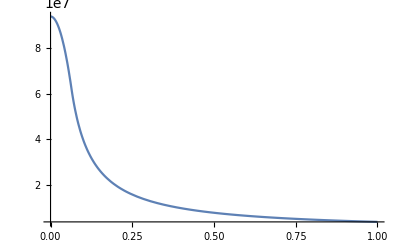

```mathematica
Plot[-Vgrav[r],{r,0,10^8},PlotRange->All]
```

```mathematica
-Vgrav[10^8]
```

3.98199×10^6

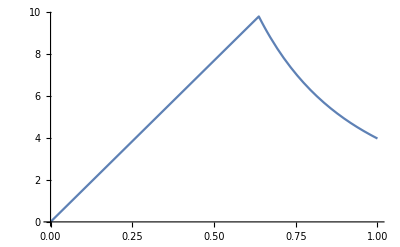

```mathematica
Plot[D[Vgrav[r],r]/.r->rt/.SIConstRepl/.EarthRepl,{rt,0,10^7}]
```

```mathematica
-D[Vgrav[r],r]
```

-(Piecewise[{{1.53985×10^-6 r, r<6371000}, {(3.98199×10^14)/r^2, r>6371000}, {Indeterminate, True}}])

#### Cross-Section scrap

```mathematica
FeTotalparams
```

{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.038×10^29,qF→1.45392×10^10,vF→1.68373×10^6,μ→1.29132×10^-18,ωp→1.81874×10^16,α→1/137,χ→0.643411,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→322.436,nI→1.2975×10^28,Z→8,M→9.27329×10^-26,EF→1.29132×10^-18,ωi→1.81874×10^16,νi→1.75116×10^16,Ai→0.209474,ωedgei→6.04519×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.91532×10^29,qF→1.78329×10^10,vF→2.06517×10^6,μ→1.94267×10^-18,ωp→2.47055×10^16,α→1/137,χ→0.580962,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→485.073,nI→2.39415×10^28,Z→8,M→9.27329×10^-26,EF→1.94267×10^-18,ωi→2.47055×10^16,νi→8.99966×10^15,Ai→0.0699144,ωedgei→6.5887×10^12},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.34359×10^29,qF→2.34292×10^10,vF→2.71326×10^6,μ→3.35328×10^-18,ωp→3.72046×10^16,α→1/137,χ→0.506851,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→837.295,nI→5.42949×10^28,Z→8,M→9.27329×10^-26,EF→3.35328×10^-18,ωi→3.72046×10^16,νi→2.01886×10^16,Ai→0.386622,ωedgei→3.02977×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→3.17873×10^30,qF→4.54874×10^10,vF→5.26776×10^6,μ→1.26398×10^-17,ωp→1.00647×10^17,α→1/137,χ→0.363758,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→3156.08,nI→3.97341×10^29,Z→8,M→9.27329×10^-26,EF→1.26398×10^-17,ωi→1.00647×10^17,νi→9.30837×10^16,Ai→0.234383,ωedgei→1.51848×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.14995×10^32,qF→2.30757×10^11,vF→2.67232×10^7,μ→3.25286×10^-16,ωp→1.14999×10^18,α→1/137,χ→0.161503,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→81222.,nI→5.18743×10^31,Z→8,M→9.27329×10^-26,EF→3.25286×10^-16,ωi→1.14999×10^18,νi→7.408×10^17,Ai→0.00108607,ωedgei→1.09042×10^18},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.0004×10^34,qF→1.05805×10^12,vF→1.2253×10^8,μ→6.83868×10^-15,ωp→1.12908×10^19,α→1/137,χ→0.0754231,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→1.70758×10^6,nI→5.00049×10^33,Z→8,M→9.27329×10^-26,EF→6.83868×10^-15,ωi→1.12908×10^19,νi→5.21962×10^18,Ai→1.38712×10^-6,ωedgei→1.09893×10^19}}

```mathematica
Total[1/("ωedgei")^3/.FeTotalparams]^-1 Total[("ne")/("ωedgei")^3/.FeTotalparams]
Total[("vF")^3/("ωedgei")^3/.FeTotalparams]^-1 Total[(("vF")^3"ne")/("ωedgei")^3/.FeTotalparams]
"ne"/.FeTotalparams
"ne"/.SiO2Totalparams
"ne"/.MgOTotalparams
```

1.91779×10^29

1.95582×10^29

{1.038×10^29,1.91532×10^29,4.34359×10^29,3.17873×10^30,4.14995×10^32,4.0004×10^34}

{4.07027×10^29,2.0121×10^30}

{1.50385×10^29,3.58115×10^29,4.37351×10^29,1.61838×10^30}

```mathematica
fFetest =Block[{InterpolationTable,LogInterpolation,vχMesh,mχMesh,meshdims,EnergyLossMesh},
mχMesh=FeλeDictSI[["mχMesh"]];
vχMesh=FeλeDictSI[["vχMesh"]];
meshdims=FeλeDictSI[["meshdims"]];
EnergyLossMesh=FeλeDictSI[["EnergyLossMesh"]];
InterpolationTable = Table[{{mχMesh[[i, j]], vχMesh[[i, j]]},
             EnergyLossMesh[[i, j]]}, {i, meshdims[["mχ"]]}, {j, meshdims[["vχ"]]
            }];
        LogInterpolation = Interpolation[Flatten[Log[10, InterpolationTable
            ], 1]]
]
(*InterpolateTable[mχMesh_,vχMesh_,meshdims_,EnergyLossMesh_] := Module[{InterpolationTable,LogInterpolation},
InterpolationTable = Table[{{mχMesh[[i, j]], vχMesh[[i, j]]},
             EnergyLossMesh[[i, j]]}, {i, meshdims[["mχ"]]}, {j, meshdims[["vχ"]]
            }];
        LogInterpolation = Interpolation[Flatten[Log[10, InterpolationTable
            ], 1]]
]*)
```

InterpolatingFunction[…]

```mathematica
fFetest[-30,5]
FeλeDictSI[["f"]][-30,5]
```

8.18039

8.18039

```mathematica
Utilities`InterpolateTable[FeλeDictSI[["mχMesh"]],FeλeDictSI[["vχMesh"]],FeλeDictSI[["meshdims"]],FeλeDictSI[["EnergyLossMesh"]]][-30,5]
```

8.18039

```mathematica
Utilities`InterpolateTable
```

```mathematica
FeλeDictSI
```

<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{6535.06,662619.,981378.,2.36555×10^7},{1.43381×10^7,1.65536×10^7,1.23976×10^8,7.76918×10^7},{3.12713×10^8,5.33698×10^8,2.34684×10^9,8.06997×10^7},{5.16717×10^9,4.43453×10^9,2.68164×10^9,8.06424×10^7},{1.02671×10^10,5.06693×10^9,2.6983×10^9,8.07682×10^7},{1.06683×10^10,5.1015×10^9,2.79759×10^9,8.01288×10^7},{1.06724×10^10,5.11093×10^9,3.00593×10^9,9.25412×10^7},{1.06736×10^10,5.11354×10^9,2.69964×10^9,7.56168×10^7}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→1.038×10^29,qF→1.45392×10^10,vF→1.68373×10^6,μ→1.29132×10^-18,ωp→1.81874×10^16,α→1/137,χ→0.643411,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→322.436,nI→1.2975×10^28,Z→8,M→9.27329×10^-26,EF→1.29132×10^-18,ωi→1.81874×10^16,νi→1.75116×10^16,Ai→0.209474,ωedgei→6.04519×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→1.91532×10^29,qF→1.78329×10^10,vF→2.06517×10^6,μ→1.94267×10^-18,ωp→2.47055×10^16,α→1/137,χ→0.580962,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→485.073,nI→2.39415×10^28,Z→8,M→9.27329×10^-26,EF→1.94267×10^-18,ωi→2.47055×10^16,νi→8.99966×10^15,Ai→0.0699144,ωedgei→6.5887×10^12},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→4.34359×10^29,qF→2.34292×10^10,vF→2.71326×10^6,μ→3.35328×10^-18,ωp→3.72046×10^16,α→1/137,χ→0.506851,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→837.295,nI→5.42949×10^28,Z→8,M→9.27329×10^-26,EF→3.35328×10^-18,ωi→3.72046×10^16,νi→2.01886×10^16,Ai→0.386622,ωedgei→3.02977×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→3.17873×10^30,qF→4.54874×10^10,vF→5.26776×10^6,μ→1.26398×10^-17,ωp→1.00647×10^17,α→1/137,χ→0.363758,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→3156.08,nI→3.97341×10^29,Z→8,M→9.27329×10^-26,EF→1.26398×10^-17,ωi→1.00647×10^17,νi→9.30837×10^16,Ai→0.234383,ωedgei→1.51848×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→4.14995×10^32,qF→2.30757×10^11,vF→2.67232×10^7,μ→3.25286×10^-16,ωp→1.14999×10^18,α→1/137,χ→0.161503,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→81222.,nI→5.18743×10^31,Z→8,M→9.27329×10^-26,EF→3.25286×10^-16,ωi→1.14999×10^18,νi→7.408×10^17,Ai→0.00108607,ωedgei→1.09042×10^18},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→4.0004×10^34,qF→1.05805×10^12,vF→1.2253×10^8,μ→6.83868×10^-15,ωp→1.12908×10^19,α→1/137,χ→0.0754231,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→1.70758×10^6,nI→5.00049×10^33,Z→8,M→9.27329×10^-26,EF→6.83868×10^-15,ωi→1.12908×10^19,νi→5.21962×10^18,Ai→1.38712×10^-6,ωedgei→1.09893×10^19}},fname→FeλeDictSI,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{10279.1,3299.03,1243.25,820.825},{2811.09,1548.58,699.647,396.878},{1166.93,319.728,448.181,334.872},{5.51771,572.613,281.017,581.269},{386.099,339.551,757.451,1049.04},{407.696,589.961,1432.4,1257.59},{724.871,876.989,1542.09,1146.8},{841.019,1652.01,1528.63,1640.58}},totalTime→40981.3|>

Choose process

```mathematica
testσselector[σs_]:=Module[{ξ2,Ps,Psums,Nσ,n},

ξ2 = Random[];

Nσ=Length[σs];
Ps=σs/Total[σs];
Psums=Table[Sum[Ps[[i]],{i,j}],{j,Length[Ps]}];

n=0;
Do[If[ ξ2<=Psums[[i]],n=i;Break[]],{i,1,Nσ}];
{n,ξ2,N[Psums]}
]
```

```mathematica
(*σstest={σ1,σ2,σ3};*)
σstest={1,2,3};
Table[Sum[σstest[[i]]/Total[σstest],{i,j}],{j,Length[σstest]}]
```

{1/6,1/2,1}

```mathematica
testσselector[{1,2,3}]
```

{2,0.485527,{0.166667,0.5,1.}}